## Leloup & Goldbeter: Circadian Oscillations

References: 
(1) Leloup JC, Goldbeter A (1999) Chaos and birhythmicity in a mdoel for circadian oscillations of the PER and TIM proteins in Drosophila. J Theor Biol 198:445-459.  doi:10.1006/jtbi.1999.0924

xCellerator implementation
created: 14 Aug 2005 BES
revised:  15 Oct 2007 BES - verify under m6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 13:46:11.055994 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

```mathematica
Clear[n];
```

```mathematica
circuit={

{CN⇄C, k2,k1}, {C->∅, kdC}, {CN->∅,kdN},
{∅⇄MP,  νsP KIP^n / (KIP^n + CN[t]^n), kd},
{MP↦∅, hill[vmax-> νmP, khalf-> KmP]},

{(∅->P0)^MP, ksP},
{P0->∅,kd},
{P1->∅,kd},
{P2->∅,kd},

{P0⇄P1,V1P/(K1P+P0[t]), V2P/(K2P+P1[t])},
{P1⇄P2, V3P/(K3P+P1[t]), V4P/(K4P+P2[t])}, 


{C->P2+T2,k4},
{T2+P2->C, k3},

{P2↦∅, hill[ vmax-> νdP, khalf-> KdP]},

{∅⇄MT, νsT*KIT^n / (KIT^n+CN[t]^n), kd+νmT/(KmT+MT[t])},

{T0⇄T1, V1T/(K1T+T0[t]), V2T/(K2T+T1[t])},
{∅⇄T0, ksT*MT[t],kd},

{T1->∅,kd},
{T1⇄T2, V3T/(K3T+T1[t]), V4T/(K4T+T2[t])},
{T2->∅,kd+νdT/(KdT+T2[t])}
};
```

```mathematica
First[interpret[circuit]]//TableForm
```

C'[t]==-k1 C[t]-k4 C[t]-kdC C[t]+k2 CN[t]+k3 P2[t] T2[t]
CN'[t]==k1 C[t]-k2 CN[t]-kdN CN[t]
MP'[t]==(KIP^n νsP)/(KIP^n+CN[t]^n)-kd MP[t]-(νmP MP[t])/(KmP+νmP MP[t])
MT'[t]==(KIT^n νsT)/(KIT^n+CN[t]^n)-MT[t] (kd+νmT/(KmT+MT[t]))
P0'[t]==ksP MP[t]-kd P0[t]-(V1P P0[t])/(K1P+P0[t])+(V2P P1[t])/(K2P+P1[t])
P1'[t]==(V1P P0[t])/(K1P+P0[t])-kd P1[t]-(V2P P1[t])/(K2P+P1[t])-(V3P P1[t])/(K3P+P1[t])+(V4P P2[t])/(K4P+P2[t])
P2'[t]==k4 C[t]+(V3P P1[t])/(K3P+P1[t])-kd P2[t]-(V4P P2[t])/(K4P+P2[t])-(νdP P2[t])/(KdP+νdP P2[t])-k3 P2[t] T2[t]
T0'[t]==ksT MT[t]-kd T0[t]-(V1T T0[t])/(K1T+T0[t])+(V2T T1[t])/(K2T+T1[t])
T1'[t]==(V1T T0[t])/(K1T+T0[t])-kd T1[t]-(V2T T1[t])/(K2T+T1[t])-(V3T T1[t])/(K3T+T1[t])+(V4T T2[t])/(K4T+T2[t])
T2'[t]==k4 C[t]+(V3T T1[t])/(K3T+T1[t])-k3 P2[t] T2[t]-(V4T T2[t])/(K4T+T2[t])-T2[t] (kd+νdT/(KdT+T2[t]))

```mathematica
parameters4SustainedOscillations={
n-> 4,
νsP-> 1, νmP-> 0.7,νdP-> 2, νsT-> 1,νmT-> 0.7,νdT-> 2, 
kd-> 0.01,
k1-> 0.6, k2-> 0.2, k3-> 1.2, k4-> 0.6, 
ksP-> 0.9, ksT-> 0.9, kdN->0.01, kdC->0.01, 
KIP-> 1,KIT-> 1,  
KmP-> 0.2,KdP-> 0.2, KmT-> 0.2, KdT->0.2,
K1P-> 2,K2P-> 2,K3P-> 2,  K4P-> 2, 
K1T-> 2, K2T-> 2,K3T-> 2, K4T-> 2, 
V1P-> 8, V2P-> 1, V3P-> 8, V4P-> 1,
V1T-> 8, V2T-> 1, V3T-> 8, V4T-> 1
}
```

{n→4,νsP→1,νmP→0.7,νdP→2,νsT→1,νmT→0.7,νdT→2,kd→0.01,k1→0.6,k2→0.2,k3→1.2,k4→0.6,ksP→0.9,ksT→0.9,kdN→0.01,kdC→0.01,KIP→1,KIT→1,KmP→0.2,KdP→0.2,KmT→0.2,KdT→0.2,K1P→2,K2P→2,K3P→2,K4P→2,K1T→2,K2T→2,K3T→2,K4T→2,V1P→8,V2P→1,V3P→8,V4P→1,V1T→8,V2T→1,V3T→8,V4T→1}

```mathematica
ic4SustainedOscillations={C->0.33,CN->1.74,MP->0.031,MT->0.031,P0->0.01,P1->0.015,P2->0.03,T0->0.01,T1->0.015,T2->0.03}
```

{C→0.33,CN→1.74,MP→0.031,MT→0.031,P0→0.01,P1→0.015,P2→0.03,T0→0.01,T1→0.015,T2→0.03}

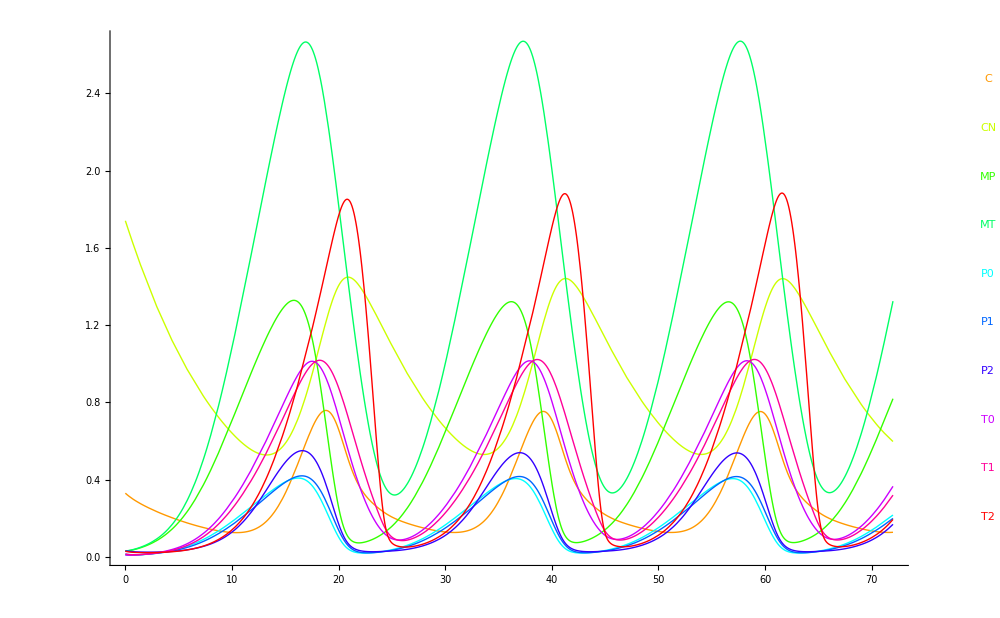

{{C→InterpolatingFunction[{{0.,72.}},<>],CN→InterpolatingFunction[{{0.,72.}},<>],MP→InterpolatingFunction[{{0.,72.}},<>],MT→InterpolatingFunction[{{0.,72.}},<>],P0→InterpolatingFunction[{{0.,72.}},<>],P1→InterpolatingFunction[{{0.,72.}},<>],P2→InterpolatingFunction[{{0.,72.}},<>],T0→InterpolatingFunction[{{0.,72.}},<>],T1→InterpolatingFunction[{{0.,72.}},<>],T2→InterpolatingFunction[{{0.,72.}},<>]}}

```mathematica
run[circuit,
rates-> parameters4SustainedOscillations,
initialConditions-> ic4SustainedOscillations,
plot-> True,
plotVariables-> {C, CN,MP,MT, P0,P1,P2, T0,T1,T2},
MaxSteps-> 5000,
timeSpan-> 72,
ImageSize-> 1000
]
```